# Performance on Trotter vs recompilation

Note: Use mathematica 12, mathematica 13 is buggy in the pattern part

```mathematica
Import["https://qtechtheory.org/questlink.m"];
SetDirectory[NotebookDirectory[]];
CreateLocalQuESTEnv["quest_link_gpu"];
```

## Modules

### Distance-related modules

```mathematica
FormatHamiltonian::usage="Format the hamiltonian from qiskit;daniel's format";
FormatHamiltonian[filename_,total_:False]:=Module[{stringham,ham,nterms,nqubits},
stringham=Import[filename];
ham=ToExpression[stringham];
nqubits=1+Select[Flatten[Level[#,-1]&/@Flatten@ham],NumericQ[#]&]//Max;
nterms=Length@ham;
If[total,
{Total@Apply[Times,ham,1],nterms,nqubits}
,
{ham,nterms,nqubits}
]
]

GetBlocks::usage="GetBlocks[blockdiagmat_,draw_:True]. Partition indices of a matrix by its blocks.";
GetBlocks[mat_,draw_:True]:=Module[{adjmat,dim=Length@mat,graph},
adjmat=ConstantArray[0,{dim,dim}];
Table[adjmat⟦i,j⟧=If[mat⟦i,j⟧==0,0,1],{i,dim},{j,dim}];
graph=AdjacencyGraph@adjmat;
If[draw,Print@graph];
ConnectedComponents@graph-1
]

CountGates::usage="CountGates[circuit], return the count for {cnots, singles}";
CountGates[circuit_]:=Module[{cnotc},
cnotc=Count[circuit/.{Subscript[C, _][_]->2,Subscript[_, _]-> 1,Subscript[_, _][_]->1},2];
{cnotc,Length@circuit-cnotc}
]

SetAttributes[MergeGates,HoldFirst]
MergeGates::usage="MergeGates[circuits], simplify circuits.";
MergeGates[circuits_]:=Module[{circc,circs,len,a,b,c,d,e,f,θ,j,i},
circs=Flatten@circuits;
While[True,
len=Length@circs;
circc=GetCircuitColumns[circuits];
circc=circc//.{
{a___,{b___,Subscript[H, j_],c___},{d___,Subscript[H, j_],e___},f___}->{a,{b,c},{d,e},f},
{a___,{b___,Subscript[Rx, j_][θ_],c___},{d___,Subscript[Rx, j_][-θ_],e___},f___}->{a,{b,c},{d,e},f},
{a___,{b___,Subscript[Rx, j_][-θ_],c___},{d___,Subscript[Rx, j_][θ],e___},f___}->{a,{b,c},{d,e},f},
{a___,{b___,Subscript[Rx, j_][θ_],c___},{d___,Subscript[Rx, j_][θ_],e___},f___}->{a,{b,Subscript[Rx, j][2θ],c},{d,e},f},
{a___,{b___,Subscript[C, j_][Subscript[X, i_]],c___},{d___,Subscript[C, j_][Subscript[X, i_]],e___},f___}->{a,{b,c},{d,e},f}
};
circs=Flatten@circc;
If[Length@circs===len,
Break[]]
];
circs
]

MatrixDist::usage="MatrixDist[matrix1, matrix2, subspace, plotglobalphase:False]. Calculate distance of 2 matrices by formula: 
                                    max_λ |Π_S(U-V)Π_S| 
                    namely, maximum absolute eigenvalues of the matrix difference projected to the subspace of interest.";
MatrixDist[M1_,M2_,subspace_,plotglobalphase_:False]:=Module[{sm1,sm2,globalphase,mindist,F,ϕ},
{sm1,sm2}=If[Length@subspace<Length@M1,{GetSubMatrix[M1,subspace],GetSubMatrix[M2,subspace]},{M1,M2}];
F[ϕ_?NumericQ]:=Max[Sqrt[Re@Eigenvalues[GetSubMatrix[ConjugateTranspose[M1-Exp[ⅈ*ϕ]M2].(M1-Exp[ⅈ*ϕ]*M2),subspace]]]];
{mindist,globalphase}=NMinimize[{F[ϕ],0≤ϕ<2π},ϕ,PrecisionGoal->5,MaxIterations->500];
If[plotglobalphase,Print@DiscretePlot[F[ϕ],{ϕ,0,2π,0.01},AxesLabel->{"ϕ","max_λ |Π_S(U-ⅇ^ⅈϕV)Π_S|"},PlotLabel->ToString@subspace]];
{mindist,ϕ/.globalphase}
]

GetSubMatrix::usage="GetSubMatrix[matrix,subspace]. Return the submatrix in the subspace.";
GetSubMatrix[matrix_,subspace_ ]:=Module[{sm,dim,x=0,y=0},
dim=Length@subspace; 
sm=IdentityMatrix[dim];
Table[
++x;y=0;
Table[
++y;
sm⟦x,y⟧=matrix⟦s+1,ss+1⟧;
,{ss,subspace}]
,{s,subspace}];
sm
]
```

### Trotterization-related modules

Reference:
https://aip.scitation.org/doi/10.1063/1.4768229

```mathematica
PauliCirc::usage="PauliCirc[coefficient, pauli_list, nqubits, prefactor]. Return the circuit of a term.";
PauliCirc[coef_,paulis_,nqubits_,factor_:1]:=Module[{circ,p,q,ngates},
If[Length@paulis>0,
circ=Table[
{p,q}=Level[c,-1];
Which[p===Z,{Subscript[C, q][Subscript[X, nqubits]]},p===X,{Subscript[Ry, q][π/2],Subscript[C, q][Subscript[X, nqubits]],Subscript[Ry, q][-π/2]},p===Y,{Subscript[Rx, q][-π/2],Subscript[C, q][Subscript[X, nqubits]],Subscript[Rx, q][π/2]}]
,{c,paulis}];
Join[circ,{{Subscript[Rz, nqubits][coef*factor]}},Reverse@circ]
,
circ={}
]
]


Propagator::usage="Propagator[coefficient, pauli_list, nqubits, prefactor]. Return the circuit of a propagator.";
Propagator[coef_,paulis_,factor_]:=Module[{lpaulis,p,q,ngates,ops,ids,rops,ropsd,rcnot,j,i,pauliops},
rops={Subscript[X, j_]->Subscript[H, j], Subscript[Y, j_]->Subscript[Rx, j][-π/2], Subscript[Z, _]->{}};
ropsd={Subscript[X, j_]->Subscript[H, j], Subscript[Y, j_]->Subscript[Rx, j][π/2], Subscript[Z, _]->{}};
rcnot={{i_Integer,j_Integer}->Subscript[C, i][Subscript[X, j]] ,{{_Integer}}->{} };
lpaulis=Table[{p,q}=Level[c,-1],{c,paulis}];
lpaulis=SortBy[lpaulis,#⟦2⟧&];
{ops,ids}={lpaulis⟦All,1⟧,Partition[lpaulis⟦All,2⟧,2,1]};
If[Length@ids<1, ids={lpaulis⟦All,2⟧}];
pauliops=Subscript[#⟦1⟧, #⟦2⟧]&/@lpaulis;
Flatten@{pauliops/.rops,ids/.rcnot,Subscript[Rz, Last@Last@ids][2*coef*factor],Reverse[ids/.rcnot],pauliops/.ropsd}
]


IsCommute::usage="IsCommute[List_paulis1, List_paulis2]. Return boolean indicates commutativity.";
IsCommute[P1_List,P2_List]:=Module[{m1,m2,nq,i},
nq=1+Max[Flatten@{P1,P2}/.Subscript[_, i_]->i];
m1=CalcCircuitMatrix[P1,nq];
m2=CalcCircuitMatrix[P2,nq];
If[Norm[m1.m2-m2.m1]≤10^-13,
True,
False]
]

PartitionPaulis::usage="ParititionPaulis[paulis], partition a list of pauli operators by commutation.";
PartitionPaulis[paulis_List]:=Module[{list1, list2},
list1={paulis⟦1⟧};list2={};
Table[
If[(AllTrue@@IsCommute[p⟦2;;⟧,#⟦2;;⟧]&/@list1)⟦1⟧,
AppendTo[list1,p],AppendTo[list2,p]]
,{p,paulis⟦2;;⟧}];
(*sanity checck*)
If[¬AllTrue[IsCommute[#⟦1⟧⟦2;;⟧,#⟦2⟧⟦2;;⟧]&/@Subsets[list1,{2}]],
Print["ERR: there is a non-commuting operation in set A"]];
If[¬AllTrue[IsCommute[#⟦1⟧⟦2;;⟧,#⟦2⟧⟦2;;⟧]&/@Subsets[list2,{2}]],
Print["ERR: there is a non-commuting operation in set B"]];
{list1,list2}
]

TrotterizeNaive::usage="TrotterizeNaive[hamiltonian_path, t, n]. Return the trotterization circuit, if full=False, it's not powered by n yet.";
TrotterizeNaive[hamfile_,t_,n_]:=Module[{ham,nqubits,nterms,r=N[t/n],estgates,esterr,circ},
{ham,nterms,nqubits}=FormatHamiltonian[hamfile,False];
ham=DeleteCases[ham,{_}]; (*delete the global phase*)
estgates=(2*Length@Flatten@ham-nterms)*n;
esterr=r^2//N;
circ=Flatten[Table[Propagator[paulis⟦1⟧,paulis⟦2;;⟧,r],{paulis,ham}],1];
Flatten@ConstantArray[circ,n]
]


Trotterize::usage="Trotterize[hamiltonian_path, t, n, order:1]. Return the trotterization circuit. Available up to the fourth order.
The paulis are partitioned into two sets A and B in which each element is commuting each other. 
Trotterization is available up to the 4th order
order 1: e^((A + B) t)=(e^(At/n)e^(Bt/n))^n+O(t Δt)
order 2: e^((A + B) t)=(e^(At/2  n)e^(Bt/n)e^(At/2  n))^n+O(t Δt^2)
order 2comp: is order 2 but compressed
order 2scb :(e^(At/2  n)e^(Bt/n)e^(At/2  n))(e^(Bt/2  n)e^(At/n)e^(Bt/2  n))(e^(At/2  n)e^(Bt/n)e^(At/2  n))
order 3: e^((A + B) t)=(e^(7/24)e^(2/3)e^(3/4)e^(-2/3)e^(-1/24)e^(Bt/n))^n+O(t Δt^3)
order 4: e^((A + B) t)=Π_(i = 1,  ... , 5)(e^p_ie^p_ie^p_i)^n+O(t Δt^4),where p1=p2=p4=p5=1/(4-4^(1/3)),p3=1-4p1
";
Trotterize[hamfile_,t_,n_,order_:1]:=Module[{ham,nterms,nqubits,list1,list2,Δt,f},
{ham,nterms,nqubits}=FormatHamiltonian[hamfile,False];
ham=DeleteCases[ham,{_}]; (*delete the global phase*)
{list1,list2}=PartitionPaulis[ham];
Which[
order===1,
f=N[t/n];
Flatten@Table[{
Table[Propagator[p⟦1⟧,p⟦2;;⟧,f],{p,list1}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,f],{p,list2}]
},{n}]
,
order===2,
f=N[0.5*t/n];
Flatten@Table[{
Table[Propagator[p⟦1⟧,p⟦2;;⟧,f],{p,list1}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,2f],{p,list2}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,f],{p,list1}]
},{n}]
,
(*compressed2 -- check if it results in the circuit order 2
template: Flatten@{e^(A/2),e^B,Table[{e^A,e^B},{n-1}],e^(A/2)}
*)
order ==="2comp",
f=N[0.5*t/n];
Flatten@{
Table[Propagator[p⟦1⟧,p⟦2;;⟧,f],{p,list1}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,2f],{p,list2}],
Table[{Table[Propagator[p⟦1⟧,p⟦2;;⟧,2f],{p,list1}],Table[Propagator[p⟦1⟧,p⟦2;;⟧,2f],{p,list2}]},{n-1}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,f],{p,list1}]
}
,
(*simon's version of order 2*)
order==="2scb",
f=N[0.5*t/n];
Flatten@Table[
If[OddQ@iter,
{Table[Propagator[p⟦1⟧,p⟦2;;⟧,f],{p,list1}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,2f],{p,list2}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,f],{p,list1}]}
,
{Table[Propagator[p⟦1⟧,p⟦2;;⟧,f],{p,list2}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,2f],{p,list1}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,f],{p,list2}]}]
,{iter,n}] (*fucking weird bug, using "i" instead of "iter" will mess up indices; I guess because I used "i" in Propagator function, but wtf? *)
,
order===3,
f=N[t/n];
Flatten@Table[{
Table[Propagator[p⟦1⟧,p⟦2;;⟧,(7/24)f],{p,list1}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,(2/3)f],{p,list2}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,(3/4)f],{p,list1}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,((-2)/3)f],{p,list2}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,((-1)/24)f],{p,list1}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,f],{p,list2}]
},{n}]
,
order===4,
f=ConstantArray[N[1/(4-4^(1/3))],5];
f⟦3⟧=N[1-4f⟦1⟧];
f=(0.5*t/n)*f;
Flatten@Table[
Flatten[Flatten@{
Table[Propagator[p⟦1⟧,p⟦2;;⟧,#],{p,list1}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,2#],{p,list2}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,#],{p,list1}]
}&/@f]
,{n}]
]
]
```

### Plots, summary modules

```mathematica
getSummary::usage="getSummary[circuit, hamiltonianMatrix, t, observedState(ground state)].
Returns {{twos-count,singles-count}, distance, ent fidelity, <e-e'>, 1-<ψ(t)|ψ'(t)>}"
getSummary[circ_,hammat_,t_,state_,subspace_:Null]:=Module[{dham,approxmat,singles,twos,dist,nqubits,space,nancilla,nconst,sbasis,entstate,entfid,eerr,fiderr,vec,vecapprox},
(*analytic matrix as reference *)
nqubits=Log2@Length@hammat;
dham=MatrixExp[-ⅈ t hammat]//Chop;
approxmat=Block[{$IterationLimit=10000},CalcCircuitMatrix[circ,nqubits]];
space=If[subspace===Null,Range[0,2^nqubits-1],subspace];
(*gates count*)
{twos,singles}=CountGates[circ];
(*distance*)
dist=MatrixDist[dham,approxmat,space];
(*entanglement infidelity*)
nconst=N[1/(√Length[space])];  
nancilla=Max[Ceiling[Log2[Length@space]],1];
sbasis=Table[space⟦idx+1⟧+2^nqubits*idx,{idx,0,Length@space-1}];
entstate=ConstantArray[0.,2^(nqubits+nancilla)];
Table[entstate⟦k+1⟧=nconst,{k,sbasis}];
entfid=1-Abs[entstate.KroneckerProduct[Inverse[approxmat].dham,IdentityMatrix[2^nancilla]].entstate]^2;
(*expected energy*)
vec=dham.state;
vecapprox=approxmat.state;
eerr=Conjugate[vecapprox].hammat.vecapprox-Conjugate[vec].hammat.vec;
(*infidelity to the true evolution state*)
fiderr=1-Abs[Conjugate[vec].vecapprox]^2;
{{twos,singles},First@dist,entfid,Re@eerr,fiderr}
]
```

getSummary[circuit, hamiltonianMatrix, t, observedState(ground state)].
Returns {{twos-count,singles-count}, distance, ent fidelity, <e-e'>, 1-<ψ(t)|ψ'(t)>}

```mathematica
ClearAll[PlotEErr]
PlotEErr[trotsum_,label_,opts_:{}]:=Module[{eerr,minval,n,idxdata},
n=Length@Keys@trotsum;
eerr=If[label===1,
Table[Table[Labeled[{i,trotsum[order][[i,4]]},Total@trotsum[order][[i,label]],Right],{i,Length@trotsum[1]}],{order,Keys@trotsum}],
Table[Table[Labeled[{i,trotsum[order][[i,4]]},NumberForm[trotsum[order][[i,label]],2],Top,FrameMargins->None,FrameStyle->Transparent,Spacings->{0, 0}],{i,Length@trotsum[1]}],{order,Keys@trotsum}]
];
minval=Min[(Join@@Values[trotsum])[[All,4]]];
ListLogPlot[eerr,LabelStyle->{FontFamily->"Asana Math",FontSize->15,Background->None},FrameLabel->{"Trotter number",TraditionalForm["ΔE"]},Frame->True,FrameStyle->{{Black,Black},{Black,Black}},PlotStyle->PointSize[Medium],PlotRange->{{0.5,2+n},{10^Floor[Log10@minval],1}},Background->White,GridLines->{None, {chemacc}},GridLinesStyle->Directive[Red, Dashed,Thick],PlotLegends->Placed[PointLegend[Automatic,( "order "<>ToString[#]&/@Range[4]),Spacings->0.1,LegendMarkerSize->5,LegendFunction->(Framed[#,FrameStyle->(Antialiasing->False)]&)],
{0.9,0.9}],opts]
]

PlotDists[trotsum_,opts_:{}]:=Module[{dists},
dists={#[[2]],#[[4]]}&/@(Join@@Values@trotsum);
ListLogLinearPlot[dists,LabelStyle->{FontFamily->"Serif",FontSize->10,Background->None},FrameLabel->{"matrix distance","ϵ_energy"},Frame->True,FrameStyle->{{Black,Black},{Black,Black}},PlotStyle->PointSize[Medium],PlotRange->Automatic,Background->White,GridLines->{None, {chemacc}},GridLinesStyle->Directive[Red, Dashed,Thick],opts]
]
```

## H_2 molecule

### Plots on Trotterizations

```mathematica
filepath="~/vqe/molecules/H2/H2.txt";
{ham,nterms,nqubits}=FormatHamiltonian[filepath,True];
(*delete the global phase*)
hammat=CalcPauliSumMatrix[DeleteCases[ham,{_}]];
eigsys=Eigensystem[hammat];
(*groundstate vector*)
gsvec=First@eigsys[[2,Ordering[eigsys[[1]],1] ]];
```

```mathematica
times={0.001,0.005,0.01,0.05,0.1,1,2,4};
```

```mathematica
times[[2;;]]
```

{0.005,0.01,0.05,0.1,1,2,4}

```mathematica
trotsum<<trotsum.mx;
trotsumsub<<trotsumsub.mx;
```

```mathematica
chemacc=1.59*10^-3;
```

#### Full space distance on trotter calculation(texted)

```mathematica
orders = {1, "2scb", 3, 4};
maxn=<|1->16,"2scb"->12,3->10,4->5|>;
trotsum = <|
   Table[
    t ->
     <|Table[
       Print["t=", t, "; order=", order];
       order ->
        Table[getSummary[MergeGates[Trotterize[filepath, t, n, order]], hammat, t, gsvec], {n, maxn[order]}], {order, orders}]|>
    , {t, times}]|>;
```

```mathematica
orders = {1, "2scb", 3, 4};
```

```mathematica
?CalcCircuitMatrix
```

```mathematica
orders = {1, "2scb", 3, 4};
maxn=<|1->56,"2scb"->36,3->18,4->5|>;
trotsum = <|
   Table[
    t ->
     <|Table[
       Print["t=", t, "; order=", order];
       order ->
        Table[getSummary[MergeGates[Trotterize[filepath, t, n, order]], hammat, t, gsvec], {n, maxn[order]}], {order, orders}]|>
    , {t, times}]|>;
```

t=0.001; order=1

NMinimize::nnum: The function value 1.431×10^-7 is not a number at {ϕ$74797394} = {0.0000970663}.

t=0.001; order=2scb

t=0.001; order=3

t=0.001; order=4

t=0.005; order=1

NMinimize::nnum: The function value 3.57749×10^-6 is not a number at {ϕ$84857665} = {0.000485331}.

NMinimize::nnum: The function value 1.78874×10^-6 is not a number at {ϕ$84865295} = {0.000485331}.

General::stop: Further output of NMinimize::nnum will be suppressed during this calculation.

t=0.005; order=2scb

t=0.005; order=3

t=0.005; order=4

t=0.01; order=1

t=0.01; order=2scb

t=0.01; order=3

t=0.01; order=4

t=0.05; order=1

t=0.05; order=2scb

t=0.05; order=3

t=0.05; order=4

t=0.1; order=1

t=0.1; order=2scb

t=0.1; order=3

t=0.1; order=4

t=1; order=1

Max::nord: Invalid comparison with 0.+8.67913×10^-10 ⅈ attempted.

Max::nord: Invalid comparison with 0.+1.18105×10^-10 ⅈ attempted.

General::stop: Further output of Max::nord will be suppressed during this calculation.

t=1; order=2scb

t=1; order=3

t=1; order=4

t=2; order=1

t=2; order=2scb

t=2; order=3

t=2; order=4

t=4; order=1

t=4; order=2scb

t=4; order=3

t=4; order=4

```mathematica
Table[trotsum[t][3]//Length,{t,times}]
```

{18,18,18,18,18,18,18,18}

```mathematica
DumpSave["trotsum.mx",trotsum];
```

```mathematica
Table[Length@trotsum[t][o],{o,{1,"2scb",3,4}},{t,times}]
```

{{56,56,56,56,56,56,56,56},{36,36,36,36,36,36,36,36},{18,18,18,18,18,18,18,18},{5,5,5,5,5,5,5,5}}

```mathematica
trotsumsub
```

<|0.001→<|1→{{{36,42},1.431×10^-7,-4.88498×10^-15,3.9746×10^-14,2.53131×10^-14},48,{{1800,2100},2.862×10^-9,-2.42473×10^-13,2.78888×10^-13,2.44693×10^-13}},2scb→{{{72,80},3,9.76996×10^-15},30,{1}},3→1,4→{1}|>,6,4→1|>
 |  |  |  |

```mathematica
Table[Length@trotsumsub[t][o],{o,{1,"2scb",3,4}},{t,times}]
```

{{56,56,56,56,56,56,56,56},{36,36,36,36,36,36,36,36},{18,18,18,18,18,18,18,18},{5,5,5,5,5,5,5,5}}

#### Subspace distance on trotter calculation(texted)

```mathematica
Table[i,{i,5,10}]
```

{5,6,7,8,9,10}

```mathematica
order="2scb";
Table[
Table[
AppendTo[trotsumsub[t][order],getSummary[MergeGates[Trotterize[filepath, t, n, order]], hammat, t, gsvec, subspace]]
,{n,33,36}]
,{t,times}]
```

NMinimize::nnum: The function value 8.61317×10^-6 is not a number at {ϕ$123081540} = {0.0970663}.

NMinimize::nnum: The function value 7.66812×10^-6 is not a number at {ϕ$123099550} = {0.0970663}.

NMinimize::nnum: The function value 0.000049839 is not a number at {ϕ$123306021} = {0.194133}.

General::stop: Further output of NMinimize::nnum will be suppressed during this calculation.

{1}
 |  |  |  |

```mathematica
subspace={3,5,6,9,10,12};
```

```mathematica
orders = {1, "2scb", 3, 4};
maxn=<|1->50,"2scb"->32,3->18,4->5|>;
trotsumsub = <|
   Table[
    t ->
     <|Table[
       Print["t=", t, "; order=", order];
       order ->
        Table[getSummary[MergeGates[Trotterize[filepath, t, n, order]], hammat, t, gsvec, subspace], {n, maxn[order]}], {order, orders}]|>
    , {t, times}]|>;
```

t=0.001; order=1

NMinimize::nnum: The function value 1.431×10^-7 is not a number at {ϕ$35103222} = {0.0000970663}.

t=0.001; order=2scb

t=0.001; order=3

t=0.001; order=4

t=0.005; order=1

NMinimize::nnum: The function value 3.57749×10^-6 is not a number at {ϕ$44234027} = {0.000485331}.

NMinimize::nnum: The function value 1.1925×10^-6 is not a number at {ϕ$44305062} = {0.000485331}.

General::stop: Further output of NMinimize::nnum will be suppressed during this calculation.

t=0.005; order=2scb

t=0.005; order=3

t=0.005; order=4

t=0.01; order=1

t=0.01; order=2scb

t=0.01; order=3

t=0.01; order=4

t=0.05; order=1

t=0.05; order=2scb

t=0.05; order=3

t=0.05; order=4

t=0.1; order=1

t=0.1; order=2scb

t=0.1; order=3

t=0.1; order=4

t=1; order=1

Max::nord: Invalid comparison with 0.+2.32831×10^-10 ⅈ attempted.

Max::nord: Invalid comparison with 0.+1.64636×10^-10 ⅈ attempted.

t=1; order=2scb

Max::nord: Invalid comparison with 0.+4.65661×10^-10 ⅈ attempted.

General::stop: Further output of Max::nord will be suppressed during this calculation.

t=1; order=3

t=1; order=4

t=2; order=1

t=2; order=2scb

t=2; order=3

t=2; order=4

t=4; order=1

t=4; order=2scb

t=4; order=3

t=4; order=4

```mathematica
DumpSave["trotsumsub.mx",trotsumsub];
```

#### Trotter full vs sub

opt[t_] := {AspectRatio -> 5/4, ImageSize -> Medium, Epilog -> Text[Style["Δt=" <> ToString[t], Medium]]}
Table[Print@Row@{PlotEErr[trotsum[t], 1, opt[t]], PlotEErr[trotsum[t], 2, opt[t]], PlotDists[trotsum[t], opt[t]]}, {t, times}];

```mathematica
t=1;
Row[{PlotEErr[trotsum[t],2,{ImageSize->{350,350},AspectRatio->9/8,Ticks->{{1,2,3,4,5}, Automatic}}],
PlotEErr[trotsumsub[t],2,{ImageSize->{350,350},AspectRatio->9/8,Ticks->None}]}]
```

```mathematica
opts[t_]:={AspectRatio->1/2,ImageSize->Medium,Epilog->Text[Style["Δt="<>ToString[t],18],Scaled[{.5,.5}]],
LabelStyle->{FontFamily->"Asana Math",FontSize->15,Background->None},FrameLabel->{"gates count","matrix distance"},Frame->True,FrameStyle->{{Black,Black},{Black,Black}},PlotStyle->PointSize[Large],Background->White,PlotLegends->Placed[PointLegend[Automatic,( "order "<>ToString[#]&/@Range[4]),Spacings->0.2,LegendMarkerSize->5,LegendFunction->(Framed[#,FrameStyle->(Antialiasing->False)]&)],
{0.8,0.7}],PlotRange->All}
```

```mathematica
Sort[Total[#]&/@trotsum[0.005][3]⟦All,1⟧]
```

{234,468,702,936,1170,1404,1638,1872,2106,2340,2574,2808,3042,3276,3510,3744,3978,4212}

```mathematica
trotsum[0.001][3]⟦All,1⟧
```

{{108,126},{216,252},{324,378},{432,504},{540,630},{648,756},{756,882},{864,1008},{972,1134},{1080,1260},{1188,1386},{1296,1512},{1404,1638},{1512,1764},{1620,1890},{1728,2016},{1836,2142},{1944,2268}}

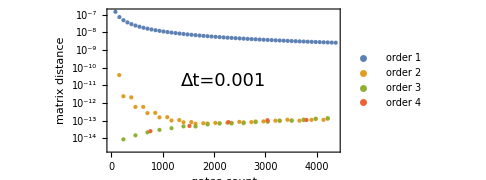
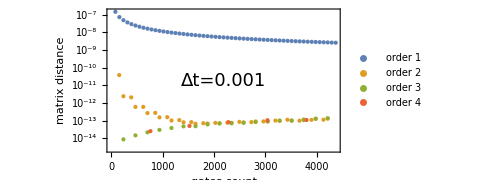
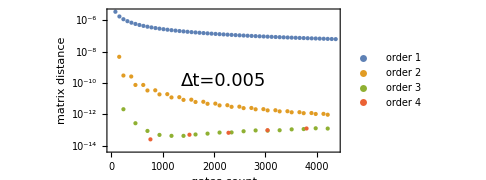
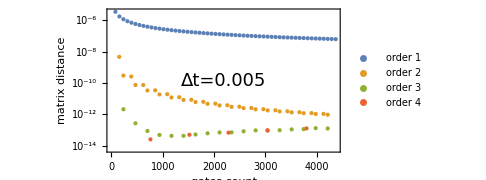
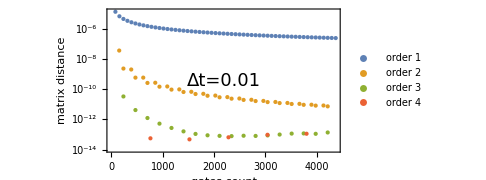
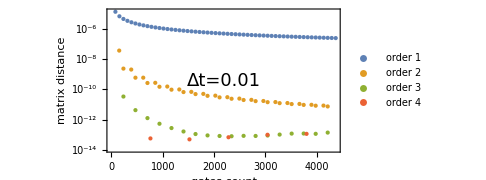
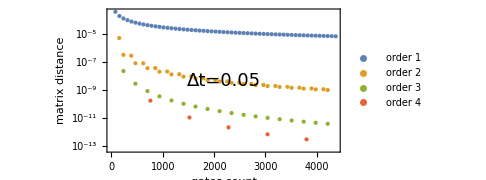
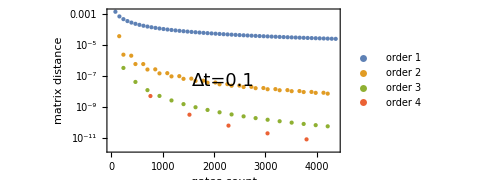
{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-}

```mathematica
Table[
Row@{ListLogPlot[Table[Transpose@{Total[#]&/@trotsumsub[t][order]⟦All,1⟧,trotsumsub[t][order]⟦All,2⟧},{order,{1,"2scb",3,4}}],opts[t]],
ListLogPlot[Table[Transpose@{Total[#]&/@trotsum[t][order]⟦All,1⟧,trotsum[t][order]⟦All,2⟧},{order,{1,"2scb",3,4}}],opts[t]]
}
,{t,times}]
```

```mathematica
Sort[Total[#]&/@trotsum[0.1][3]⟦All,1⟧]
```

{234,468,702,936,1170,1404,1638,1872,2106,2340,2574,2808,3042,3276,3510,3744,3978,4212}